```mathematica
(*test*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\benjamin\Documents\FPII\Moessbauer\code

```mathematica
files=FileNames["*.TKA",{"../data/background"}]
```

{../data/background\021mm.TKA,../data/background\1mm.TKA,../data/background\2mm.TKA,../data/background\3mm.TKA,../data/background\8mm_no_ab.TKA,../data/background\8mm.TKA}

```mathematica
?String
```

String is the head of a character string "text".

```mathematica
FullForm[files[[1]]]
```

"../data/background\021mm.TKA"

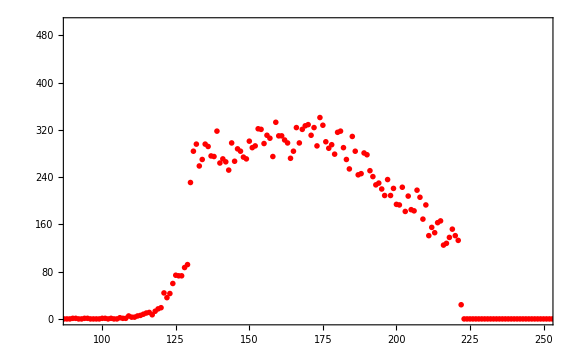
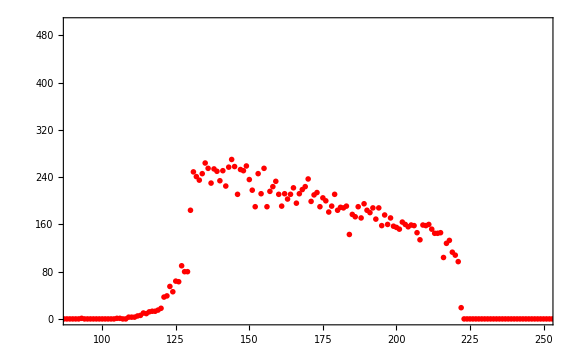
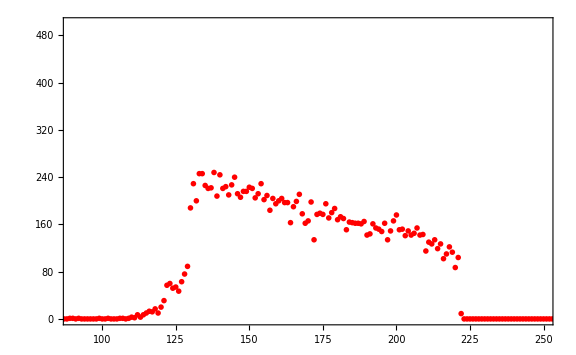
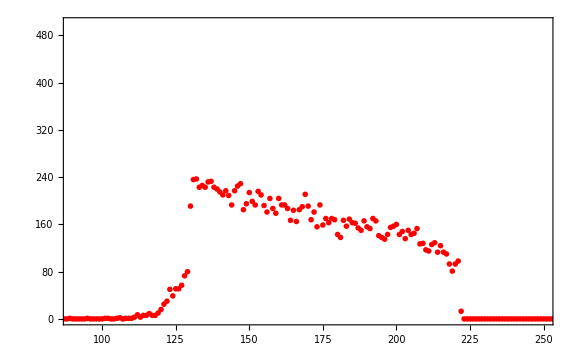
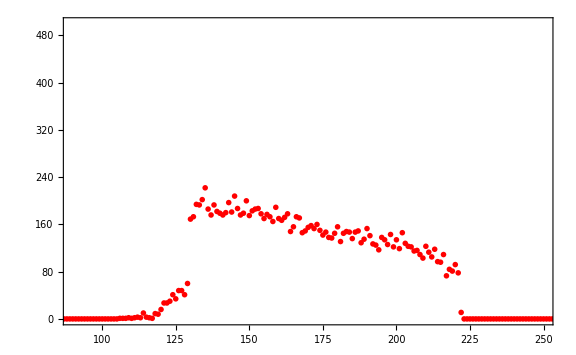
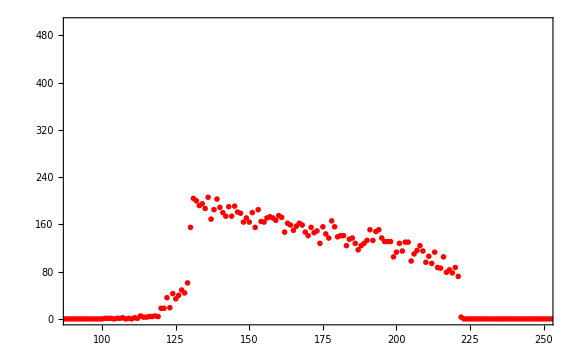

```mathematica
ListPlot[Flatten[Import[#,"CSV"]],PlotRange->{{90,250},{0,500}}, ImageSize -> Large,Frame->True,PlotStyle-> Red]&/@files
```

```mathematica
data=Flatten[Import["../data/background\\8mm_no_ab.TKA","CSV"]];
ListPlot[data,PlotRange->{{90,250},{0,500}}, ImageSize -> Large,Frame->True,PlotStyle-> Red]
n=Sum[data[[90;;250]][[i]],{i,1,160}]
Print["Zählrate ",n/600.0]
```

-Graphics-

14213

Zählrate 23.6883

```mathematica
?Print
```

Print[expr] prints expr as output.

```mathematica
Sqrt[13786]//N
```

117.414

```mathematica
Sqrt[14213]//N
```

119.218